# Methods Bound Reference

## Usage Guide and Syntax

### Syntax

Basic Operations + - * /
Shift+Enter to execute
Ctrl+/ for fraction - a/b
a^b for exponents or ctrl+6 - a^b
Capital letters for first letter of each word in a command
Square brackets surrounding the contents of a command
Double == for solving
Single = for defining variables
Square Root - crtl+2
Escape -> deg -> Escape gives degree °
Escape then other things such as pi then escape for symbols.

### Algebraic Commands

#### Solve/SolveAlways

Solves an equation or system of equations for it/s variable/s. Solve[LHS==RHS, variable]
e.g.

```mathematica
Solve[3x+10==40,x]
```

{{x→10}}

```mathematica
Solve[{y==15-x,y==2x+10},{x,y}]
```

{{x→5/3,y→40/3}}

SolveAlways finds values of parameters so that lhs = rhs

```mathematica
SolveAlways[]
```

#### Reals

Add on to solve to limits solutions to real numbers only.
e.g.
Without Reals

```mathematica
Solve[2^x==4,x]
```

{{x→ConditionalExpression[(2 ⅈ π C[1])/Log[2]+Log[4]/Log[2], C[1]∈ℤ]}}

With Reals

```mathematica
Solve[2^x==4,x, Reals]
```

{{x→2}}

#### Simplify / Full Simplify

Changes an expression to a more simple form, usually collecting like terms and taking out common factors
e.g.

```mathematica
Simplify[3(x-2)^2+3x+1/2(x+2)^2]
```

7/2 (4-2 x+x^2)

FullSimplify - Similar to simplify but sometimes goes further to make it possible more simple.
e.g.

```mathematica
FullSimplify[3(x-2)^2+3x+1/2(x+2)^2]
```

7/2 (4+(-2+x) x)

#### Expand

Expands out any brackets then collects like terms.
e.g.

```mathematica
Expand[3(x-2)^2+3x+1/2(x+2)^2]
```

14-7 x+(7 x^2)/2

#### Reduce

Reduces the statement to solve inequalities and find domains.
e.g.

```mathematica
Reduce[4x-1>11]
```

x>3

#### Clear

Clears the variable within the square brackets if that variable has been defined
e.g.

```mathematica
x=2
```

2

```mathematica
x
```

2

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
(*Clears All*)
ClearAll["Global`*"]
```

#### Defining a function

Defines the function, in this case f. Can be used for plotting, solving or other things.

```mathematica
f[x_]:=2x-3
```

```mathematica
f[0]
```

-3

```mathematica
f[2x]
```

-3+4 x

```mathematica
Solve[f[x]==0,x]
```

{{x→3/2}}

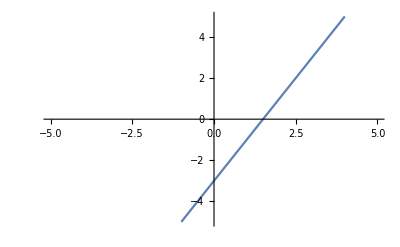

```mathematica
Plot[f[x],{x,-5,5},PlotRange->{-5,5}]
```

```mathematica
Clear[f]
```

#### Breaking fractions apart

Separating and simplifying fractions

```mathematica
Solve[x==2/(3y-1),y]
```

{{y→(2+x)/(3 x)}}

```mathematica
Solve[x==2/(3y-1),y]//Apart
```

{{y→1/3+2/(3 x)}}

### Graphing Commands

#### Plot

Plots the graph of y=__: Plot[RHS, {variable (x), lowest value to display, highest value to display}]
e.g. To plot the graph of y=x^2

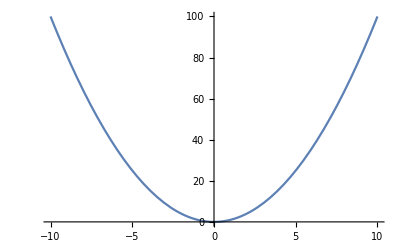

```mathematica
Plot[x^2,{x,-10,10}]
```

#### PlotRange

Add on to Plot to choose what y-values to display
e.g.

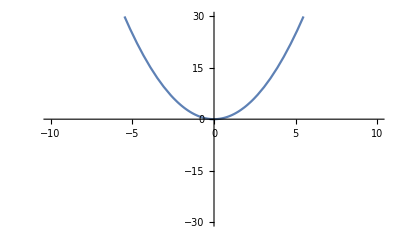

```mathematica
Plot[x^2,{x,-10,10},PlotRange->{-30,30}]
```

#### ContourPlot

Can plot any relation ContourPlot[LHS==RHS,{x,xmin,xmax},{y,ymin,ymax},Axes->True, Frame->False]
e.g.

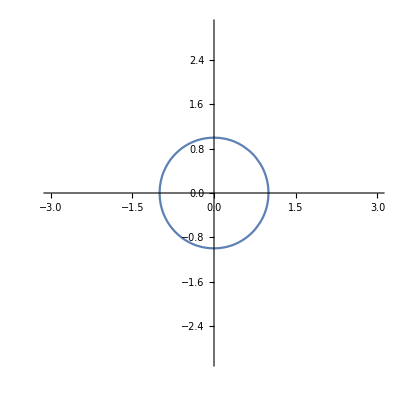

```mathematica
ContourPlot[y^2+x^2==1,{x,-3,3},{y,-3,3},Axes->True,Frame->False]
```

#### AspectRatio

Use to chose the aspect ratio of a graph.
e.g.

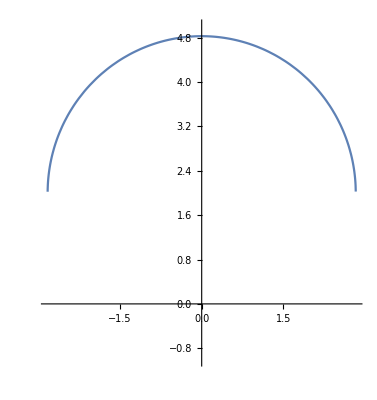

```mathematica
Plot[2+√(8-x^2),{x,-5,5},PlotRange->{-1,5},AspectRatio->Automatic]
```

#### Manipulate

Goes around another function to add a slider for a variable.
e.g. in a graph

```mathematica
Manipulate[Plot[{√x-1/4,x+k},{x,-5,5}, PlotRange->{-4,4}],{k,-5,5}]
```

### Trigonometric Commands

#### Trig Ratios

Sin Cos Tan (Radians is default) Arc is the inverse.

```mathematica
Sin[30Degree]
```

1/2

```mathematica
ArcCos[1/2]/(π/180)
```

60

### Quadratic Commands

### Other Commands

#### Binomial

Binomial Finds the amount of combinations for Vlaues n and r Binomial[n,r]
Below shows the possible combinations of lottery numbers. (1-45, 6 numbers)

```mathematica
Binomial[45,6]
```

8145060

### Common Errors

Within the solve function you must use == instead of =.
Variables already defined when trying to solve.
Mistyping an equation.
Put a space or * between variables to avoid creating a new variable.

## Functions, Relations and Transformations

### Domain, Range and Notation

Domain - The domain is all the possible values shown on the x-axis.
Range - The Range is all the possible values shown on the y-axis.
Set Notation - A notation that includes a collection of elements. 
e.g. If x was any of the integers from 1-5 it would be notated as x ∈ {1,2,3,4,5}.
Other Terminology - R is a term meaning all real numbers, R^+means all positive real numbers not including zero, R^- means all negative real numbers not including zero. You can use this to notate domain and range. ∩ - Means intersect/and. ∪ - Union/or. ∈ - Means element. \ - Means without.
R Notation - If there was a graph of a truncus with no transformations, the Domain would be x ∈ R \ {0}, the Range would be y ∈ R^+
Interval Notation - Pronumeral ∈ [ or ( Lower Bound, Upper Bound ) or ]
e.g. x is larger than -2 but less than or equal to 5. x ∈ (-2,5]
Function Notation - {Pronumeral: Lower Bount < or \[VectorLessEqual] Pronumeral > or \[VectorGreaterEqual] Upper Bound} 
e.g. x is larger than -2 but less than or equal to 5. {x: -2 < x \[VectorGreaterEqual] 5}
Function notation: f:D->ℝ,f(x)=(insert rule here), Where:
D = the domain for which the function works
ℝ = the co-domain, the set of all possible outcomes of the function.

Finding the domain of a function

```mathematica
FunctionDomain[x^2,x]
```

True

Finding the range of a function

```mathematica
FunctionRange[x^2,x,y]
```

y≥0

### Types of Relations

#### Functions:

Functions are a type of relation that are either one-to-one or many-to-one. The vertical line test can be used to determine if a relation is a function.

#### One-to-One (Function):

Each x-value maps onto a unique y-value. Passes the vertical and horizontal line test.

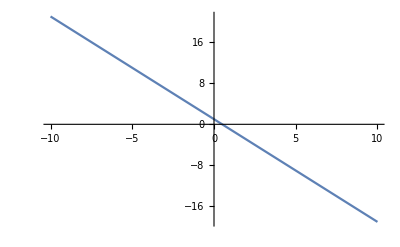

```mathematica
Plot[-2x+1, {x,-10,10}]
```

#### Many-to-One (Function):

More than one x-value maps onto the same y-value. Passes the vertical line test.

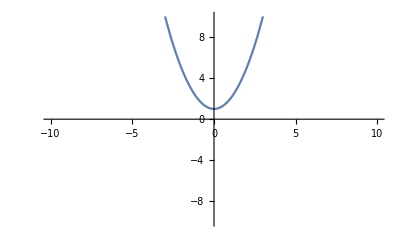

```mathematica
Plot[x^2+1, {x,-10,10}, PlotRange->{-10,10}]
```

#### Relation:

A relation is any link between x and why values. Functions are all relations, but not all relation are functions.

#### One-to-Many (Relation):

An x-value maps onto more than one y-values.

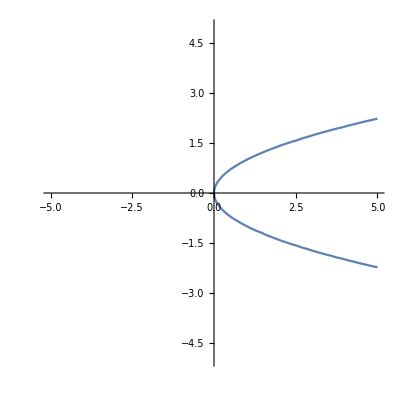

```mathematica
ContourPlot[x==y^2,{x,-5,5},{y,-5,5},Axes->True,Frame->False]
```

#### Many-Many: (Relation)

More than one x-value maps onto more than one y-value.

```mathematica
ContourPlot[y^2+x^2==1,{x,-3,3},{y,-3,3},Axes->True,Frame->False]
```

-Graphics-

### Function Transformation Summary

a, n, h and k are used for transformations.
a : af(x) : dilation by a factor of a from the x axis
n : f(nx) : dilation by a factor of 1/n from the y axis
if a is negative : -f(x) : reflection in the x axis
if n is negative : f(-x) : reflection in the y axis
h : f(x-h) :  translation h units in the positive x direction
k : f(x) + k : translated k units in the positive y direction

#### Hyperbola

y=a/(x-h)+k - asymptotes occur at x=h and y=k

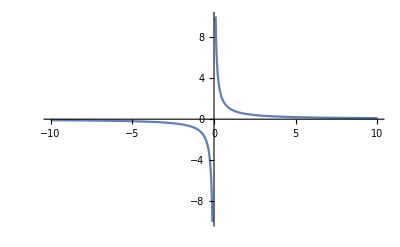

```mathematica
Plot[1/x,{x,-10,10}, PlotRange->{-10,10}]
```

#### Truncus

y = a/(n(x-h))^2+k - asymptotes occur at x=h and y=k

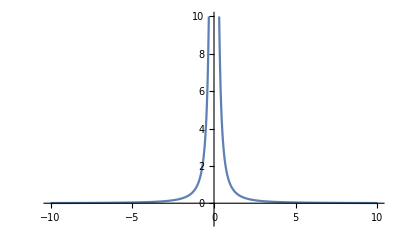

```mathematica
Plot[1/x^2,{x,-10,10},PlotRange->{-1,10}]
```

#### Square root graph

y = a √(n(x-h)) +k - start/end point at (h,k)

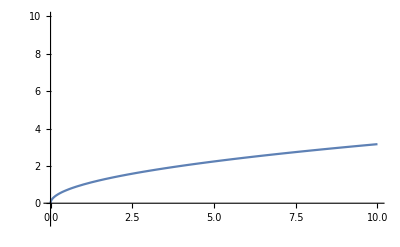

```mathematica
Plot[√x,{x,-1,10},PlotRange->{-1,10}]
```

#### Circle graph

(x-h)^2+(y-k)^2=r^2 - centre point at (h,k), radius is r
Other Form - x^2+ y^2-2hx-2ky+c=0 (where c = h^2+k^2-r^2)

```mathematica
ContourPlot[y^2+x^2==1,{x,-3,3},{y,-3,3},Axes->True,Frame->False]
```

-Graphics-

#### Semicircle graph

y= √(r^2-(x-h^2)) + k - centre point at (h,k), radius is r

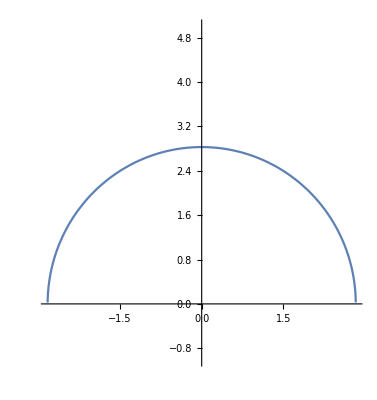

```mathematica
Plot[√(8-x^2),{x,-5,5},PlotRange->{-1,5},AspectRatio->Automatic]
```

## Linear Relations and Equations

Tips/mistakes: 
- When solving questions for values of m in parallel or perpendicular lines, look at the gradient only

### Linear graphs

Converting radians to degrees: 
degrees to radians: Multiply by π/180
radians to degrees: Divide by π/180

When finding the angle a line makes with the positive x-axis, if it has a negative gradient, you must subtract that angle from 180 to get the right angle.
Distance formula: D=√((y_2-y_1)^2+(x_2+x_1)^2)
Gradient: Rise/Run

#### Parallel lines

m_1=m_2

#### Perpendicular lines

m_1 m_2=-1

## Probability and Counting Methods

### Basic Definitions and Information

#### Sample Space and Events

-Graphics-

#### Complementary Events

-Graphics-

### Probability

To show something as a subset: A⊂B means that A is a subset of B.
∅ = null set
Rules of probability for finite sample spaces:
- Pr(A) greater or equal to 0
- Pr(A) less than or equal to 1 
- Sum of probabilities of all outcomes = 1
- The more trials, the closer the outcomes get to the theoretical probability
- Addition rule: Probability of A or B both occurring is calculated by: Pr(A∪B)=Pr(A)+Pr(B)-Pr(A∩B)

Complementary events
When 2 events have no elements in common and together make up the entire sample space. The complement of event A is A', this consists of all outcomes in the sample space that aren’t A:
Pr(A')=1-Pr(A)

Independent events
Events which are not conditional, one occurring does not affect the probability other.
Pr(A∩B) = Pr(A)*Pr(B)
Pr(A|B) = Pr(A)
Mutually exclusive events are different to independent events. Mutually exclusive means the 2 events occurrence can not be simultaneous

Conditional probability 
Pr(A|B): Probability of A given B has occurred or (n(events of A contained in B))/(n(B))
Formula: Pr(A|B) = (n(A∩B))/(n(B)) or (Pr(A∩B))/(Pr(B))

### Visualising probability

Tree diagrams
Venn diagrams
-Graphics-

-Graphics-

Karnaugh maps/probability tables
An alternative to venn diagrams. Imagine a venn diagram, it can be represented by a Karnaugh map:
 		□ | B | B'
A | A∩B | A∩B'
A' | A'∩B | A'∩B'
 In a Karnaugh map, the entries give the probability of each of these events occurring.
 The sets A∩B and A∩B' are mutually exclusive, so:
 Pr(A∩B)+Pr(A∩B')=Pr(A) (row 1), similarly:
 Pr(A'∩B)+Pr(A'∩B')=Pr(A') (row 2)
Pr(A∩B) + Pr(A'∩B)=Pr(B) (column 1)
Pr(A∩B')+Pr(A'∩B')=Pr(B') (column 2)
 
 Since Pr(A)+Pr(A')=1 and Pr(B)+Pr(B')=1, the totals for column 3 and row 3 are 1. The completed table is:

□ |  B | B' | □
A | A∩B | A∩B' | Pr(A)
A' | A'∩B | A'∩B' | Pr(A')
□ | Pr(B) | Pr(B') | 1

## Quadratics

### Basic Quadratic Commands

Factorising:
Done when an equation is in general form y=ax^2+bx+c to turn it into the root form (x-a)(x-b)
When done by hand, there are 4 methods used to factorise an equation.
	1. By sight
	2. Coat-Hanger Method
	3. Completing the square
	4. Quadratic Formula
After an equation is factorised into root form, ‘a’ and ‘b’ in (a,0) and (b,0) are the x-intercepts

Expanding:
Done when an equation is in root form or in vertex form to convert it to general form.


Below are the ways to do the above in Mathematica:

```mathematica
(*Remember double =, and the final pronumeral is what you are solving it for*)
Solve[(2x+3)/4==7,x]
```

{{x→25/2}}

```mathematica
(*To solve an inequality, use reduce then finish it like solve*)
Reduce[(-2x+3)/4>=1,x]
```

x≤-1/2

```mathematica
Simplify[(a^2+b^2)/4-(a+b)^2/4]
```

-(a b)/2

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Expand[2(x+6)^2+10]//TraditionalForm
```

2 x^2+24 x+82

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

Plotting Equations:

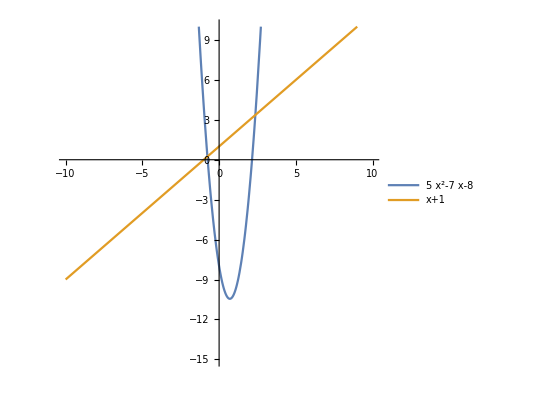

```mathematica
Plot[{5 x^2-7x-8,x+1},{x,-10,10},PlotRange->{-15,10},AspectRatio->1,PlotLegends->"Expressions"]
```

### Locating Axis Intercepts

The x-intercept is usually found through root form that is (x-a)(x-b) where (0,a) and (0,b) are the x-intercepts.
For a quadratic equation,  there can be 0, 1 or 2 x-intercepts.
To determine the number of solutions/x-intercepts within a quadratic equation, the discriminant formula (b^2-4ac) is used.

```mathematica
(*For a known coefficient*)
Discriminant[4 x^2+10x+7,x]
```

-12

```mathematica
(*For an unknown coefficient*)
(*MAKE SURE THERE IS A SPACE BETWEEN m AND x TO REGISTER IT AS TWO DIFFERENT VARIABLES*)
(*If x is black, that means it is already defined and must be cleared with Clear[x]*)
Discriminant[10 x^2+3m x+7,x]
```

-280+9 m^2

To find the actual x-intercept, use solve.

```mathematica
Solve[(2x+3)/4==-7,x]
```

{{x→-31/2}}

```mathematica
Solve[a x + c == b x - d,x]
```

{{x→(-c-d)/(a-b)}}

--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
On the other hand, the y-intercept is found through general form ax^2+bx+c, where (0,c) is the y-intercept.
For a quadratic equation, there is always 1 y-intercept.
To find the y-intercept, do below.

```mathematica
4x+7/.x->0
```

7

```mathematica
f[x_]:=4x+7
f[0]
```

7

### Finding the Turning point

Usually when finding the turning point of an equation, the equation in general form will be converted into vertex form.
E.g. ax^2+bx+c -> (a(x-k))^2+h
The turning point from there is (k,h)
Below are some ways that can be done in Mathematica
________________________________________________________________________________________________________________________________________________________________________________

Method 1: FindMinimum or FindMaximum
Use FindMinimum when a  > 0 and the parabola is upwards
Use FindMaximum when a < 0 and the parabola is downwards

```mathematica
FindMinimum[4 x^2+10x+7,x]
```

{0.75,{x→-1.25}}

```mathematica
FindMaximum[-2 x^2-8x+5/2,x]//Rationalize
```

{21/2,{x→-2}}

Method 2: Subbing in -b/(2a) 
With the form ax^2+bx+c, find -b/(2a) and sub it into the original equation as x.

```mathematica
(*Let y=5 x^2-7x-8*)
(-(-7))/(2(5))
```

7/10

```mathematica
5 x^2-7x-8/.x->7/10
```

```mathematica
-209/20
(*Therefore Turning point = (7/10,-209/20)*)
```

Method 3: Find the middle of the x-intercepts and sub it into the equation.

```mathematica
(*Let y=5 x^2-7x-8*)
Solve[5 x^2-7x-8==0,x]
```

{{x→1/10 (7-√209)},{x→1/10 (7+√209)}}

```mathematica
(1/10 (7-√209)+1/10 (7+√209))/2//Simplify
```

7/10

```mathematica
5 x^2-7x-8/.x->7/10
```

```mathematica
-209/20
(*Therefore Turning point = (7/10,-209/20)*)
```

Method 4: Completing the square

```mathematica
(*Let y=x^2+2x+4*)
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
```

```mathematica
compsq[1,2,4]
```

(x+1)^2+3

### Points of Intersection

When trying to find the line of intersection between 2 linear equations, you can use simultaneous equations.
Although you are able to do the same with a quadratic and a linear equation, you will get 2 answers most of the time in root form (x-a)(x-b)
When doing it in Mathematica, set the equations equal to one another via the y, then solve for both x and y.
E.g.

```mathematica
Solve[{y==5 x^2-7x-8,y==x+1},{x,y}]
```

{{x→1/5 (4-√61),y→1/5 (9-√61)},{x→1/5 (4+√61),y→1/5 (9+√61)}}

Therefore the Point’s of Intersection are ((4 - √61)/5,(9-√61)/5) and ((4 + √61)/5,(9+√61)/5)
Graphed, the two equations look like this:

```mathematica
Plot[{5 x^2-7x-8,x+1},{x,-10,10},PlotRange->{-15,10},AspectRatio->1,PlotLegends->"Expressions"]
```

-Graphics-

### Determining Quadratic Rules with unknowns

For three unknowns:
Let the unknown coordinates be (1, -4), (-1, 10) and (3, -2)

```mathematica
Clear[f,x]
f[x_]:=a x^2 + b x + c
Solve[f[{1,-1,3}]=={-4,10,-2},{a,b,c}]
```

{{a→2,b→-7,c→1}}

For one unknown and two x intercepts:
x-intercepts, (2, 0) and (-3, 0) <--> Passing point (4,5)

```mathematica
(*y=a(x-x1)(x-x2)
Sub in the two x intercept x coordinates for x1 and x2
Finally sub in the known point and solve for a in root form*)
Solve[4==a(x-2)(x+3),a]/.x->5
```

{{a→1/6}}

Therefore the full equation is 1/6(x-2)(x+3) = y

### Test Questions

Distance Formula:

```mathematica
EuclideanDistance[{5,2},{0,4}]
```

√29

The values of m for which the parabola y =  m x^2 + x + 3 intersects with the linear graph y = m x + 2 exactly two times is:

```mathematica
Solve[m x^2+x+3==m x + 2,x]
(*Find Discriminant*)
Reduce[1-6 m+m^2>0,m]
```

{{x→(-1+m-√(1-6 m+m^2))/(2 m)},{x→(-1+m+√(1-6 m+m^2))/(2 m)}}

m<3-2 √2||m>3+2 √2

The graph  y = 2 x^2 + a x + 3 ,   where  - 2 √6 < a ≤  2 √6   could have how many x-intercepts?

```mathematica
2 √6//N
Manipulate[Plot[2 x^2 + a x + 3 ,{x,-10,10},PlotRange->{-10,10}],{a,-4.89898,4.89898}]
```

4.89898

## Cubics and Quartics

### Polynomial Division

Polynomial Division - gives the quotient(value when one thing is divided by the other) and remainder in the form of {quotient, remainder}

```mathematica
PolynomialQuotientRemainder[x^4+2 x+1,x^2+1,x]
```

{-1+x^2,2+2 x}

Polynomial Remainder - gives the remainder and ignores the quotient

```mathematica
PolynomialRemainder[x^4+2 x+1,x^2+1,x]
```

2+2 x

Polynomial Quotient - gives the quotient, dropping the remainder (ignoring it)

```mathematica
PolynomialQuotient[x^4+2 x+1,x^2+1,x]
```

-1+x^2

Polynomial Division - Greatest common factor (if output is 1 the 2 polynomials are relatively prime, meaning they share no common positive factors other than 1)

```mathematica
PolynomialGCD[(1+x)^2 (2+x) (4+x),(1+x) (2+x) (3+x)]
```

(1+x) (2+x)

Lowest Common multiple for 2 or more Polynomials

```mathematica
PolynomialLCM[(1+x)^2 (2+x) (4+x),(1+x) (2+x) (3+x)]
```

(1+x)^2 (2+x) (3+x) (4+x)

Cancel out common factors

```mathematica
(x^2-1)/(x-1)
```

(-1+x^2)/(-1+x)

```mathematica
Cancel[%]
```

1+x

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

### Solving for Variables

```mathematica
SolveAlways[6*x^3-7 x^2-x+2==(x-1)(a*x^2+b*x+c),x]
```

{{a→6,b→-1,c→-2}}

Find a solution for x (x-int) that is near 1.5. (Similar to bisection method)

```mathematica
FindRoot[x^3-x-2,{x,1.5}]
```

{x→1.52138}

### Domains

Domain on a graph (simple method)

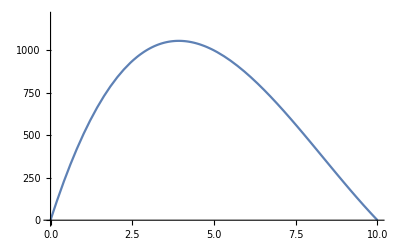

```mathematica
Plot[x(20-2x)(30-2x),{x,0,10},PlotRange->{-10,1200}]
```

Domain on a graph (more complicated way -> shows more of the axes but keeps domain the same)

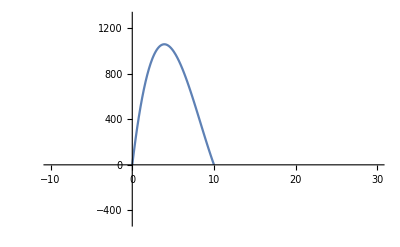

```mathematica
Plot[x(20-2x)(30-2x),{x,0,10},PlotRange->{{-10,30},{-500,1300}}]
```

### Maximums and Minimums

Finds a maximum between the x values of 0 and 10

```mathematica
FindMaximum[4 x^3-100 x^2+600x,{x,0,10}]
```

{1056.31,{x→3.92375}}

Finds a maximum near the x value of 4

```mathematica
FindMaximum[4 x^3-100 x^2+600x,{x,4}]
```

{1056.31,{x→3.92375}}

```mathematica
Plot[4 x^3-100 x^2+600x,{x,0,10},PlotRange->{-10,1200}]
```

-Graphics-

### Equation Forms

Cubics:
(what you can see), other features it has

(y-int): ax^3+bx^2+cx+d
(SPI),1 x-int: a(x-h)^3+k
(3 x-ints), 2 TPs: a(x-b)(x-c)(x-d)
(2 x-ints, 1 TP),1 TP: a(x-b)(x-c)^2
(1 x-int),1 SPI/PI: a(x-b)(cx^2+dx+e)

Quartics:

(y-int): ax^4+bx^3+cx^2+dx+e

Sum of Cubes:A^3-B^3=(A+B)(A^2-AB+B^2)
Difference of Cubes: A^3-B^3=(A-B)(A^2+AB+B^2)

### Stationary Points Nature

Sign Table:

```mathematica
f[x_]:=x^3-11 x^2+24x
Solve[f'[x]==0]
TableForm[{x,f'[x]}/.x->{1,4/3,2},TableHeadings->{{"x","f'(x)"},None}]
```

{{x→4/3},{x→6}}

x | 1 | 4/3 | 2
f'(x) | 5 | 0 | -8

## Inverse Functions

### Rooting (Cubes or more)

Fixing Issue with ,Reals in Solve (expresses outputs with powers)

```mathematica
Solve[x==(2y-3)^3-4,y,Reals]
```

{{y→Root[-31-x+54 #1-36 #1^2+8 #1^3&,1]}}

```mathematica
Solve[x==(2y-3)^3-4,y,Reals]//ToRadicals
```

{{y→1/2 (3+(4+x)^(1/3))}}

### Making an inverse function

Swap x and y then solve for y (use apart if you want the fractions separate)
y=1/(x-3)

```mathematica
Solve[x==1/(y-3),y]//Apart
```

{{y→3+1/x}}

Inverse Mathematica function (may not always work)

```mathematica
f[x_]:=1/(x-3)
```

```mathematica
InverseFunction[f][x]
```

(1+3 x)/x

Sometimes can give a goofy answer so use //N

```mathematica
f[x_]:=Log[2,5x]
g[x_]:=InverseFunction[f][x]
g[x]//N
```

ConditionalExpression[0.2 2.^x, -3.14159<0.693147 Im[x]≤3.14159]

### Plotting with domain restriction for inverse function

Plotting with restriction for inverse function (&& for domain restriction, range difficult) (may need to find range of original function for domain of inverse)
Change PlotRange from {-10,10} to 10 to make the axes x = -10 to 10

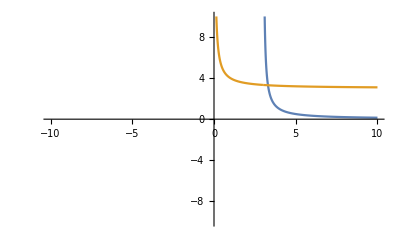

```mathematica
Plot[{1/(x-3)&&x>3,1/x+3&&x>0},{x,-10,10},PlotRange->10]
```

## Logs and Exponentials

Logs have vertical asymptotes, exponentials have horizontal asymptotes

### Exponential Functions

2^x: _/ ,2^-x: \_, -2^x: ‾\, -2^-x: /‾
Base Change: logₐ(x)=logₑ(x)/logₑ(a)
Examples of Exponential functions

```mathematica
n[t_]:=80+20*2^t
```

Starts at 100 and goes up -> 120, 160, 240, 400...

### Logarithmic Functions

Log₂(x): |‾, Log₂(-x): ‾|, -Log₂(-x): _|, -Log₂(x): |_
If there is a factor:

```mathematica
10*Log[10,p/10^-12]
```

10(Log[10,p]-Log[10,10^-12])

10*Log[10, p] - 10(-12*1)

10*Log[10, p] + 120

Solving Logs

```mathematica
Log[4,64]
```

3

```mathematica
Solve[Log[4,x]==3,x]
```

{{x→64}}

```mathematica
Solve[Log[x,64]==3,x]
```

{{x→4}}

Figuring out answers with variables

```mathematica
FullSimplify[Log[10,a^2]+Log[10,b^2]-Log[10,(a*b)^2],Assumptions->{a>0,b>0}]
```

0

or

```mathematica
Assuming[a>0&&b>0,FullSimplify[Log[10,a^2]+Log[10,b^2]-Log[10,(a*b)^2]]]
```

0

## Circular Functions/Trig

Rem:
Period: 
Tan = π/n, where Tan(n*x)
Cos and Sin = (2π)/n, where Sin(n*x)
Amplitude:
a where a*Sin(x)
Asymptote:
Tan[...], where ... = π/2

### Solving for x in sin, cos, tan

sin(x) and cos(x) can only have solutions -1<=x<=1 as the unit circle has no points where x is > 1
Solve with domain

```mathematica
Solve[Cos[x]==1/2&&0<=x<=4π,x,Reals]
```

{{x→π/3},{x→(5 π)/3},{x→(7 π)/3},{x→(11 π)/3}}

```mathematica
h[t_]:=21.8 +20Sin[(π*t)/12]
```

Reduce with domain

```mathematica
Reduce[{h[t]≥  11.8,0≤ t≤ 24},t]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤t≤14.||22.≤t≤24.

### Tan

Finding Asymptotes, x-ints,y-ints, etc

```mathematica
f[x_]:=Tan[x-π/4]+1
```

Ints

```mathematica
f[0]
```

0

Use && For Domain

```mathematica
Solve[f[x]==0&&-π<=x<=π,x]
```

{{x→0},{x→-π},{x→π}}

Finding the Period (T)

```mathematica
FunctionPeriod[f[x],x]
```

π

Domain and Range

```mathematica
FunctionDomain[f[x],x]
```

1/2+(π/4-x)/π∉ℤ

```mathematica
FunctionRange[f[x],x,y]
```

True

Asymptote for Tan only (Add period for more) Tan(x)=π/2, x= asymptote

```mathematica
Solve[x-π/4==π/2,x]
```

{{x→(3 π)/4}}

Graphing (Ticks is domain (v1 and v2) and increments (v3) labelling), Exclusions gets rid of the blue asymptote lines

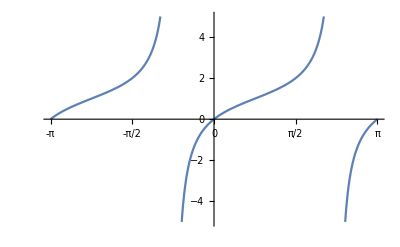

```mathematica
Plot[f[x],{x,-π,π},PlotRange->5,Ticks->{Range[-π,π,π/4],Automatic}, GridLines->{{-π/4,3 π/4},None},GridLinesStyle->Directive[Red,Dashed], Exclusions->{-π/4,3 π/4}]
```

### Complementary Angles and Pythag Identity

Sin[π/2-x]=Cos[x]
Sin[π/2+x]=Cos[x]
Cos[π/2-x]=Sin[x]
Cos[π/2+x]=-Sin[x]

Cos^2[x]+Sin^2[x]=1

### Cleaner Answers Using FullSimplify

```mathematica
Solve[Tan[2x]==-1+√2&&-π<x<π,x]
```

{{x→1/2 (-2 π-ArcTan[1-√2])},{x→1/2 (-π-ArcTan[1-√2])},{x→1/2 (π-ArcTan[1-√2])},{x→-1/2 ArcTan[1-√2]}}

```mathematica
Solve[Tan[2x]==-1+√2&&-π<x<π,x]//FullSimplify
```

{{x→-(15 π)/16},{x→-(7 π)/16},{x→(9 π)/16},{x→π/16}}

### Exact Values

### Visualising the Triangle

Sin(t)=1/3, find (Cos(t))/(Tan(t))
o/h = 1/3 meaning a is √(3^2-1)= 2 √2
Cos is a/h = (2 √2)/3 and Tan is o/a = 1/(2 √2)
Therefore (Cos(t))/(Tan(t))= ((2 √2)/3)/(1/(2 √2)) = 8/3

```mathematica
Simplify[((2 √2)/3)/(1/(2 √2))]
```

8/3

## Substituting Values

finds values of y where x is {...} values

```mathematica
f[x_]:=x^2+4
f[x]/.x->{0,1/2}
```

{4,17/4}

Table, x and y values between 0 and 6 at increments of 1/2

```mathematica
Table[{x,f[x]},{x,0,6,1/2}]//TableForm
```

0 | 4
1/2 | 17/4
1 | 5
3/2 | 25/4
2 | 8
5/2 | 41/4
3 | 13
7/2 | 65/4
4 | 20
9/2 | 97/4
5 | 29
11/2 | 137/4
6 | 40

## Rates of Change/Differentiation

### Limits

Correct syntax when writing on paper:
f’(x) = lim  10x + 5h -3
	 h->0
	then write = 10x -3 when sub in h (get rid of the lim syntax)

Limits (Indeterminate means undefined)

```mathematica
Limit[x^2+2,x->1]
```

3

```mathematica
Limit[1/x,x->0]
```

Indeterminate

Left and right limits (FromAbove for right limit, FromBelow for left limit)

```mathematica
Limit[1/x,x->0,Direction->"FromAbove"]
```

∞

```mathematica
f[x_]:=x^2-5x
```

```mathematica
Limit[(f[x+h]-f[x])/h,h->0]
```

-5+2 x

### Derivatives

f’(x) = derivative

Finding Derivative

```mathematica
D[x^2,x]
```

2 x

Inserting f’(x) = 0 gives the x values of the stationary points (can also determine how many)

Once x is found, sub x value into f(x) not f’(x) as f’(x) will = 0

```mathematica
l[x_]:=x^2+1
```

```mathematica
{x,l[x]}/.Solve[l'[x]==0,x,Reals]
```

{{0,1}}

Do not use /.->Solve because Solve already has arrows.

### Chain Rule

(x^3 + 2)^2
let u = inner function e.g. x^3 + 2
du/dx is the derivative of the inner function e.g. 3 x^2
dy/du is the derivative of the outer function e.g. 2(x^3 + 2)^1
Multiply dy/du and du/dx to get dy/dx

Note: if the variable is the denominator e.g. 1/((x^2+1)^3) make it 1*(x^2 + 1)^-3 before applying the chain rule.

### Normals and Tangent Equations (Custom functions and formula)

Tangent line of (x1,y1):
y-y1=f’(x1)(x-x1)

eqn is the equation and 1 is the x value at which the tangent/normal intersects

```mathematica
TangentLine[eqn_,a_]:=Expand[Solve[y-(eqn/.x->a)==(D[eqn,x]/.x->a)(x-a),y]]
```

```mathematica
TangentLine[x^2,1]
```

{{y→-1+2 x}}

Normal lines:
y-y1=-1/(f'(x1))(x-x1)

```mathematica
NormalLine[eqn_,a_]:=Expand[Solve[y-(eqn/.x->a)==(-1/D[eqn,x]/.x->a)(x-a),y]]
```

```mathematica
NormalLine[x^2,1]
```

{{y→3/2-x/2}}

```mathematica
v[x_]:=2 x^3+4 x^2
L[x_,a_]:=v'[a](x-a)+v[a]
K[x_,a_]:=-1/v'[a](x-a)+v[a]
Manipulate[Plot[{v[x],L[x,a],K[x,a]},{x,-5,5},PlotRange->{-5,5},AspectRatio->1],{a,-2,2}]
```

### Plotting Derivatives (Custom Functions)

Custom Function

```mathematica
PlotDerivative[func_,{x_,xmin_,xmax_}]:=Module[{df},df=D[func,x];Plot[{func,df},{x,xmin,xmax},PlotLegends->{"Function","Derivative"},AxesLabel->{"x","y"},PlotStyle->{Blue,Red}]]
```

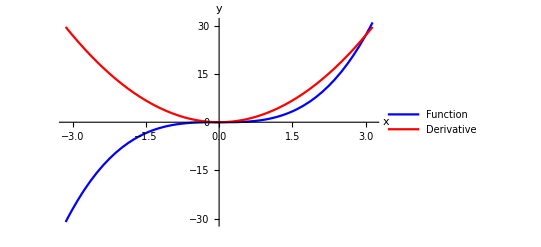

```mathematica
PlotDerivative[x^3,{x,-π,π}]
```

### Finding Stationary Points

Inserting f’(x) = 0 gives the x values of the stationary points (can also determine how many)
Once x is found, sub x value into f(x) not f’(x) as f’(x) will = 0

Finds the coordinates of stationary points:

```mathematica
v[x_]:=x^2+1
```

```mathematica
{x,v[x]}/.Solve[v'[x]==0,x,Reals]
```

{{0,1}}

Do not use /.->Solve because Solve already has arrows.

Sign Table

```mathematica
q[x_]:=x^3-11 x^2+24x
```

```mathematica
q'[x]/.x->{1,4/3,2,6,7}
```

{5,0,-8,0,17}

or (more fancy)

```mathematica
TableForm[{x,q'[x]}/.x->{1,4/3,2,6,7},TableHeadings->{{"x","q'(x)"},None}]
```

x | 1 | 4/3 | 2 | 6 | 7
q'(x) | 5 | 0 | -8 | 0 | 17

### Proportion Rule

d/dx(f/g) = (g*f'-f*g')/g^2

E.g. (5+3x)/(x^2+7)
f=5+3x,f'=3,g=x^2+7,g'=2x
=(-3 x^2-10x+21)/((x^2+7)^2)

### Newton’s Method

For estimating x ints
1 Trial: x2 = x1 - f[x1]/f'[x1]
eqn is the function, var is “x” or the x variable in the function, x is the starting number
The custom function below is only 1 trial.

```mathematica
Newton[eqn_,var_,x_]:=x-(eqn/.var->x)/(D[eqn,var]/.var->x)
```

```mathematica
y[x_]:=x^2-2
Newton[y[x],x,2]
```

3/2

Other version:
Input:

```mathematica
ClearAll[f,x,nit]
f[x_]:=2 x^3+25 x^2-5x-125          (* Insert the function f(x) *)
x[0]:=2                (* Insert the value of x[0]. x[0] is the initial guess Subscript[x, 0] for the solution to f(x)=0 *)
nit:=5                 (* nit is the number of iterations *)
```

Algorithm

```mathematica
Do[x[n+1]=x[n]-(f[x[n]])/(D[f[x],x]/.x->N[x[n]]),{n,0,N[nit]}]          (* Note: x[n] represents Subscript[x, n]. x[0] is the value of Subscript[x, 0] *)
Style[Row[{"Approximate solution to ",f[x],"= 0 after ", nit ," iterations is ",N[x[nit],9]}],FontColor->Blue]    (* Value of Subscript[x, n+1] after n=nit iterations *)
Clear[Dist1]
Dist1=Table[{n,N[x[n]],f[x[n]]},{n,1,N[nit]}]//N;
Grid[Prepend[Dist1,{"Iteration","   Approximate solution","f[x]"}]] (*generates a table of the approximate solution and the y value of the function at that x value*)
```

Approximate solution to -125-5 x+25 x^2+2 x^3= 0 after 5 iterations is 2.15238

Iteration |    Approximate solution | f[x]
1. | 2.15966 | 0.951365
2. | 2.1524 | 0.00200217
3. | 2.15238 | 8.93581×10^-9
4. | 2.15238 | 0.
5. | 2.15238 | 0.

## Surds/Nth Roots

### Nth Root Syntax

the 4th root of 3 (= 3^(1/4))

```mathematica
3 x^2-1/x^2/.x->-1/Surd[3,4]
```

0

## Piecewise/hybrid functions

Defining and Plotting

(exclusions gets rid of all points at x = 0 -> the weird mathematica line)

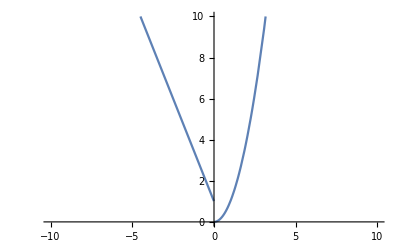

```mathematica
k[x_]:=Piecewise[{{x^2,x>=0},{-2x+1,x<0}}]
Plot[k[x],{x,-10,10},PlotRange->{0,10},Exclusions->0]
```

Other Method (esc pw esc then ctrl enter)

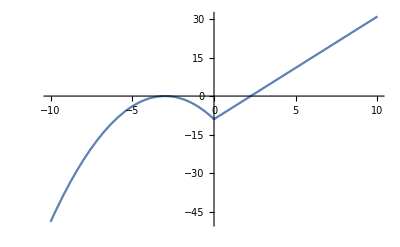

```mathematica
Plot[Piecewise[{{-(x+3)^2, x<=0}, {4x-9, x>0}}],{x,-10,10}]
```

Limits

```mathematica
Limit[k[x],x->0,Direction->"FromAbove"]
Limit[k[x],x->0,Direction->"FromBelow"]
```

0

1

## Things to Remember

1. READ THE QUESTION CAREFULLY
2. Exact values unless specified otherwise
3. Round to the specified amount of significant figures
4. Remember to add units 
5. Show your work
6. Use sentences when needed (e.g. ∴ the number of chickens is 5)
7. Switch inequality signs when divide or multiply by a negative number
8. Some answers have restrictions (graphs and values)
9. Diameter and Radius are different (they may try to trick you by asking for diameter after you use a formula for radius e.g. πr^2)
10. Remember axes change e.g. t axis instead of x axis (when talking about translations)
11. Be careful of negatives (in brackets, fractions, etc)
12. Remember you can use let e.g. let a = √x to get a quadratic
13. In Inverse functions, asymptotes swap equations and domain and range swap
14. Use the quadratic formula when dealing with bad values: (-b+-√(b^2-4ac))/(2a)
15. With domains for x in Sin(x) = (+-5)/3, check what quadrant the domain is and whether Sin is positive or negative
16. Inside of logs cannot be >= 0, so when you find solutions, check they work
17. Simplify expressions
18. May need to use , Reals and //N in logs and exponents

Full Function Notation: f: domain->codomain(R),f(x)=x^2+2x+1
codomain is always R in methods